```mathematica
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"../src/MultipleScattering2D.wl"];
```

### Scattering from one cylinder

```mathematica
impulse[τ_]= ⅇ^(-5(τ-1)^2);
options=Sequence["Impulse"-> impulse,"ImpulsePeriod"->2.,"PrintChecks"-> False,"Boundary"-> "Neumann","FrequencyModes"->20,"NAngularModes"->4];
options=Sequence["Impulse"-> impulse,"ImpulsePeriod"->2.,"PrintChecks"-> False,"Boundary"-> "Dirichlet","FrequencyModes"->26,"NAngularModes"->4];
data= AcousticScattering[0.5,{0.,2.5},{1.,6.,0.2},{4.,.2,.2},options];
(*Usage*)
(*AcousticScattering[radius,sourcePosition,{Subscript[t, 0],Subscript[t, max],δt},{Subscript[R, max],δR,δθ}];*)
(*AcousticScattering[radius,sourcePosition,t,{Subscript[R, max],δR,δθ}]*)

(*Note*)
(*Flatten[data,2]; will produce a list where each element is {t,θ,r,wave[t,θ,r]]}. *)
```

```mathematica
(*And this is how you make a gif!*)
lps=PlotWaves[data];
Export[NotebookDirectory[]<>"WaveS.gif",lps]
```

Max Amp: 0.109425

/home/art/uom/study/Scattering/ScatterCylinder/v2/examples/WaveS.gif

```mathematica
data=txθxrxwS;
Export[NotebookDirectory[]<>"WaveS2.CSV",data,"CSV"];
```

{δω,Ω}: {1.39626,27.9253}

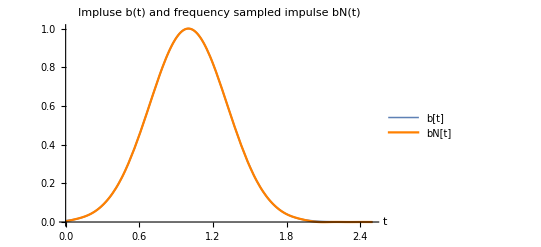

```mathematica
(*Here is some data "WaveS.CSV" ready to use*)
data=ToExpression[Import[NotebookDirectory[]<>"WaveS.CSV","CSV"]];
```